```mathematica
table=Import["C:\\Users\\alexn\\Documents\\GitHub\\Labs\\Photonics_Labs\\Laser Engraving\\data.xlsx"];
```

```mathematica
table1=table[[1]];
```

```mathematica
table1//Grid
```

I, A | U, ,v | nakachka, mvt | gener
14. | 165. | 2. | 2310.
14.2 | 166. | 2. | 2357.2
14.4 | 166. | 2. | 2390.4
14.6 | 167. | 2. | 2438.2
14.7 | 167. | 11. | 2454.9
14.8 | 167. | 23. | 2471.6
14.9 | 168. | 38. | 2503.2
15. | 168. | 54. | 2520.
15.1 | 168. | 72. | 2536.8
15.2 | 169. | 95. | 2568.8
15.3 | 169. | 116. | 2585.7
15.4 | 169. | 131. | 2602.6
15.5 | 170. | 152. | 2635.
15.6 | 170. | 170. | 2652.
15.7 | 170. | 194. | 2669.
15.8 | 171. | 218. | 2701.8
15.9 | 171. | 254. | 2718.9
16. | 171. | 284. | 2736.
16.1 | 172. | 320. | 2769.2
16.2 | 172. | 354. | 2786.4
16.3 | 172. | 386. | 2803.6
16.4 | 173. | 425. | 2837.2
16.5 | 173. | 464. | 2854.5
16.6 | 173. | 490. | 2871.8
16.7 | 174. | 538. | 2905.8
16.8 | 174. | 599. | 2923.2
16.9 | 175. | 642. | 2957.5
17. | 175. | 690. | 2975.
17.1 | 176. | 736. | 3009.6
17.2 | 176. | 790. | 3027.2
17.3 | 176. | 835. | 3044.8
17.4 | 177. | 884. | 3079.8

```mathematica
For[i=2,i≤ Length[table1],i++,
table1[[i,1]]=Quantity[table1[[i,1]],"Amperes"];
table1[[i,2]]=Quantity[table1[[i,2]],"Millivolts"];
table1[[i,3]]=Quantity[table1[[i,3]],"Milliwatts"];
table1[[i,4]]=Quantity[table1[[i,4]],"Watts"];
]
```

```mathematica
table2=table[[2]]
```

{{I,U,nakacha,gener},{14.4,167.,2.,2404.8},{14.5,167.,14.,2421.5},{14.6,168.,35.,2452.8},{14.7,168.,51.,2469.6},{14.8,168.,69.,2486.4},{14.9,169.,85.,2518.1},{15.,169.,102.,2535.},{15.1,169.,121.,2551.9},{15.2,170.,140.,2584.},{15.3,170.,161.,2601.},{15.4,170.,182.,2618.},{15.5,171.,203.,2650.5},{15.6,171.,232.,2667.6},{15.7,171.,257.,2684.7},{15.8,172.,284.,2717.6},{15.9,172.,297.,2734.8},{16.,172.,325.,2752.},{16.1,172.,357.,2769.2},{16.2,173.,397.,2802.6},{16.3,173.,432.,2819.9},{16.4,174.,470.,2853.6},{16.5,174.,511.,2871.},{16.6,174.,531.,2888.4},{16.7,174.,562.,2905.8},{16.8,175.,602.,2940.},{16.9,175.,641.,2957.5},{17.,175.,686.,2975.},{17.1,176.,727.,3009.6},{17.2,176.,772.,3027.2},{17.3,176.,810.,3044.8},{17.4,177.,854.,3079.8}}

```mathematica
For[i=1,i≤ Length[table2],i++,
table2[[i,1]]=Quantity[table2[[i,1]],"Amperes"];
table2[[i,2]]=Quantity[table2[[i,2]],"Millivolts"];
table2[[i,3]]=Quantity[table2[[i,3]],"Milliwatts"];
table2[[i,4]]=Quantity[table2[[i,4]],"Watts"];
]
```

```mathematica
Graph1=LinearModelFit[Transpose[Reverse[Transpose[QuantityMagnitude[table1]]]][[6;;All,1;;2]],x,x]["BestFit"]
```

-3546.02+1.41517 x

```mathematica
Graph2=LinearModelFit[Transpose[Reverse[Transpose[QuantityMagnitude[table2]]]][[2;;All,1;;2]],x,x]["BestFit"]
```

-3112.57+1.26661 x

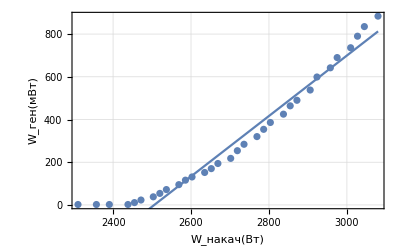

```mathematica
Show[ListPlot[Transpose[Reverse[Transpose[table1]]][[All,1;;2]],PlotTheme->"Detailed",Frame->True,FrameLabel->{"W_(:043d:0430:043a:0430:0447)(Вт)","W_(:0433:0435:043d)(мВт)"}],Plot[Graph1,{x,2404,3080}]]
```

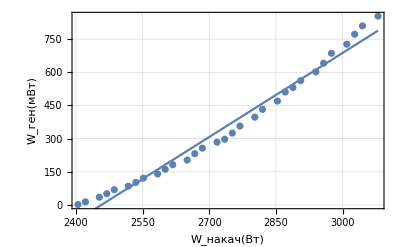

```mathematica
Show[ListPlot[Transpose[Reverse[Transpose[table2]]][[All,1;;2]],PlotTheme->"Detailed",Frame->True,FrameLabel->{"W_(:043d:0430:043a:0430:0447)(Вт)","W_(:0433:0435:043d)(мВт)"}],Plot[Graph2,{x,2404,3080}]]
```

```mathematica
Graph1
```

-3546.02+1.41517 x

```mathematica
Graph2
```

-3112.57+1.26661 x

```mathematica
LinearModelFit[Transpose[Reverse[Transpose[QuantityMagnitude[table1]]]][[6;;All,1;;2]],x,x]["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -3546.02 | 125.459 | -28.2644 | 4.76789×10^-21
x | 1.41517 | 0.0453996 | 31.1714 | 4.01337×10^-22

```mathematica
LinearModelFit[Transpose[Reverse[Transpose[QuantityMagnitude[table2]]]][[6;;All,1;;2]],x,x]["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -3361.69 | 95.4939 | -35.2032 | 8.01539×10^-23
x | 1.35351 | 0.0342893 | 39.4733 | 4.8094×10^-24

```mathematica
Solve[Graph1==0,x]
```

{{x→2505.73}}

```mathematica
Solve[Graph2==0,x]
```

{{x→2457.41}}

```mathematica
QuantityMagnitude[table2]//TeXForm
```

\left(
\begin{array}{cccc}
 \text{I} & \text{U} & \text{nakacha} & \text{gener} \\
 14.4 & 167. & 2. & 2404.8 \\
 14.5 & 167. & 14. & 2421.5 \\
 14.6 & 168. & 35. & 2452.8 \\
 14.7 & 168. & 51. & 2469.6 \\
 14.8 & 168. & 69. & 2486.4 \\
 14.9 & 169. & 85. & 2518.1 \\
 15. & 169. & 102. & 2535. \\
 15.1 & 169. & 121. & 2551.9 \\
 15.2 & 170. & 140. & 2584. \\
 15.3 & 170. & 161. & 2601. \\
 15.4 & 170. & 182. & 2618. \\
 15.5 & 171. & 203. & 2650.5 \\
 15.6 & 171. & 232. & 2667.6 \\
 15.7 & 171. & 257. & 2684.7 \\
 15.8 & 172. & 284. & 2717.6 \\
 15.9 & 172. & 297. & 2734.8 \\
 16. & 172. & 325. & 2752. \\
 16.1 & 172. & 357. & 2769.2 \\
 16.2 & 173. & 397. & 2802.6 \\
 16.3 & 173. & 432. & 2819.9 \\
 16.4 & 174. & 470. & 2853.6 \\
 16.5 & 174. & 511. & 2871. \\
 16.6 & 174. & 531. & 2888.4 \\
 16.7 & 174. & 562. & 2905.8 \\
 16.8 & 175. & 602. & 2940. \\
 16.9 & 175. & 641. & 2957.5 \\
 17. & 175. & 686. & 2975. \\
 17.1 & 176. & 727. & 3009.6 \\
 17.2 & 176. & 772. & 3027.2 \\
 17.3 & 176. & 810. & 3044.8 \\
 17.4 & 177. & 854. & 3079.8 \\
\end{array}
\right)

```mathematica
table3=table[[3]]
```

{{I,U,t,},{17.4,177.,0.38,3079.8},{17.2,176.,0.33,3027.2},{17.,176.,0.34,2992.},{16.8,175.,0.34,2940.},{16.6,175.,0.38,2905.},{16.4,174.,0.42,2853.6},{16.2,173.,0.34,2802.6},{16.,173.,0.37,2768.},{15.8,172.,0.42,2717.6},{15.6,171.,0.45,2667.6},{15.4,170.,0.54,2618.},{15.2,170.,0.52,2584.},{15.,169.,0.56,2535.},{14.8,169.,0.7,2501.2},{14.6,168.,0.84,2452.8}}

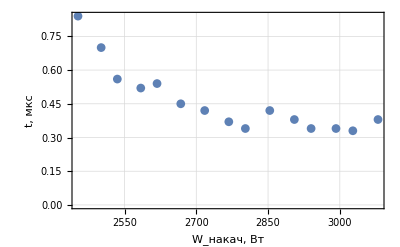

```mathematica
ListPlot[Transpose[Reverse[Transpose[table3]]][[2;;All,1;;2]],PlotTheme->"Detailed",PlotMarkers->Automatic, Frame->True, FrameLabel->{"W_(:043d:0430:043a:0430:0447), Вт","t, мкс"}]
```

```mathematica
table3//TeXForm
```

\left(
\begin{array}{cccc}
 \text{I} & \text{U} & \text{t} & \text{} \\
 17.4 & 177. & 0.38 & 3079.8 \\
 17.2 & 176. & 0.33 & 3027.2 \\
 17. & 176. & 0.34 & 2992. \\
 16.8 & 175. & 0.34 & 2940. \\
 16.6 & 175. & 0.38 & 2905. \\
 16.4 & 174. & 0.42 & 2853.6 \\
 16.2 & 173. & 0.34 & 2802.6 \\
 16. & 173. & 0.37 & 2768. \\
 15.8 & 172. & 0.42 & 2717.6 \\
 15.6 & 171. & 0.45 & 2667.6 \\
 15.4 & 170. & 0.54 & 2618. \\
 15.2 & 170. & 0.52 & 2584. \\
 15. & 169. & 0.56 & 2535. \\
 14.8 & 169. & 0.7 & 2501.2 \\
 14.6 & 168. & 0.84 & 2452.8 \\
\end{array}
\right)